```mathematica
(*question no 3*)
```

```mathematica
Exit[]
```

```mathematica
setA=Disk[{0,0},1];
setB=Disk[{1.3,0},1];
setC=Disk[{1.3,0.75},1];
```

```mathematica
(*a*)
```

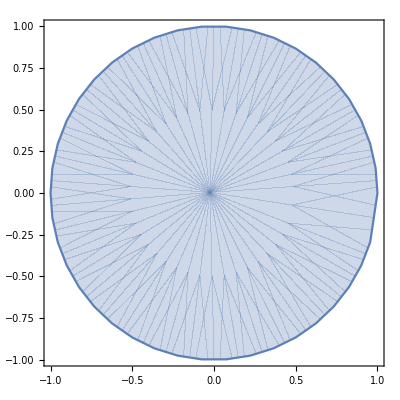

```mathematica
RegionPlot[setA]
```

```mathematica
(*b*)
```

```mathematica
RegionPlot[]
```

RegionPlot::argr: RegionPlot called with 1 argument; 3 arguments are expected.

RegionPlot[{setA&&setB}]

```mathematica
diskA[x_,y_]:=x^2+y^2=1;
diskB[x_,y_]:=(x-1.3)^2+y^2=1;
diskC[x_,y_]:=(x-1.3)^2+(y-0.75)^2=1;
```

```mathematica
RegionPlot[diskA[x,y],{x,1,3},{y,1,3}]
```

Set::write: Tag Plus in x^2+y^2 is Protected.

Set::write: Tag Plus in 1.00021+1.00021 is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

-Graphics-

```mathematica
(*Question No 08*)
```

```mathematica
num={6944,7245,21408};
Table[{n,Divisible[n,2],Divisible[n,3],FactorInteger[n]},{n,num}]//TableForm[#,TableHeadings->{None, {"Number","Divisible by 2","Divisible by 3","Primefactorization"}},TableAlignments->Center]&
```

Number | Divisible by 2 | Divisible by 3 | Primefactorization
6944 | True | False | 2 | 5
7 | 1
31 | 1
7245 | False | True | 3 | 2
5 | 1
7 | 1
23 | 1
21408 | True | True | 2 | 5
3 | 1
223 | 1

```mathematica
(*Question No 09*)
```

```mathematica
number={41,43,107,113};
Table[{n,PrimeQ[n]&&PrimeQ[FromDigits[Reverse[IntegerDigits[n]]]]&&FromDigits[Reverse[IntegerDigits[n]]]!=n},{n,number}]//TableForm[#,TableHeadings->{None, {"Number","Emirp"}},TableAlignments->Center]&
```

Number | Emirp
41 | False
43 | False
107 | True
113 | True

```mathematica
(*Question No 10*)
```

```mathematica
a=Input[a];
b=Input[b];
g=GCD[a,b]
l=LCM[a,b]
product1=a*b
product2=g*l
conjecture=product1==product2
```

24

144

3456

3456

True

```mathematica
(*Question No 11*)
```

```mathematica
Clear[skyClear,sundown,seeSaturn]
```

```mathematica
exp1=Implies[skyClear&&sundown,seeSaturn];
exp2=Implies[!skyClear||!sundown,!seeSaturn];
Table[{skyClear,sundown,seeSaturn,exp1,exp2},{skyClear,{True,False}},{sundown,{True,False}},{seeSaturn,{True,False}}]//Flatten[#,2]&//TableForm[#,TableHeadings->{None, {"skyclear","sundown","seeSaturn","exp1","exp2"}}]&
```

skyclear | sundown | seeSaturn | exp1 | exp2
True | True | True | True | True
True | True | False | False | True
True | False | True | True | False
True | False | False | True | True
False | True | True | True | False
False | True | False | True | True
False | False | True | True | False
False | False | False | True | True

```mathematica
(*Question No 12*)
```

```mathematica
Exit[]
```

```mathematica
Clear[fedex,ups,ontime]
```

```mathematica
stat1=fedex->!ups&&ontime;
stat2=ontime<->fedex||!ups;
stat3=Implies[!fedex,!ups&&ontime];
Table[{fedex,ups,ontime,stat1,stat2,stat3},{fedex,{True,False}},{ups,{True,False}},{ontime,{True,False}}]//Flatten[#,2]&//TableForm[#,TableHeadings->{None, {"Fedex","UPS","ontime","statement 1","statement 2","statement 3"}},TableAlignments->Center]&
```

Fedex | UPS | ontime | statement 1 | statement 2 | statement 3
True | True | True | True→False | True<->True | True
True | True | False | True→False | False<->True | True
True | False | True | True→True | True<->True | True
True | False | False | True→False | False<->True | True
False | True | True | False→False | True<->False | False
False | True | False | False→False | False<->False | False
False | False | True | False→True | True<->True | True
False | False | False | False→False | False<->True | False

```mathematica
(*Question No 13*)
```

```mathematica
gradpoint[n_]:=Piecewise[{
{4.0,n>=80},
{3.75,75<=n<=79},
{3.5,70<=n<=74},
{3.25,65<=n<=69},
{3.0,60<=n<=64},
{2.75,55<=n<=59},
{2.5,50<=n<=54},
{2.25,45<=n<=49},
{2.0,40<=n<=44},
{0.0,n<40}
}];
```

```mathematica
Exit
```

```mathematica
(*Question No 03*)
```

```mathematica
cirA[x_,y_]:=x^2+y^2=1;
cirB[x_,y_]:=(x-1.3)^2+y^2=1;
cirC[x_,y_]:=(x-1.3)^2+(y-0.75)^2=1;
(*a*)
```

```mathematica
RegionPlot[cirA[x,y],{x,-1,3},{y,-1,3}]
```

Set::write: Tag Plus in x^2+y^2 is Protected.

Set::write: Tag Plus in 0.999579+0.999579 is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

-Graphics-